## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)

(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/fourier/singles/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.185578 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Mar 14, 2020, time: 22:43:48

nb: /Users/dantopa/Mathematica_files/nb/ert/rcs/fourier/singles/sigma(nu).nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.185578 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
fticks={{Automatic,Automatic},{{{1,-π},{91,-π/2},{181,0},{271,π/2},{361,π}},Automatic}};
nticks={{Automatic,Automatic},{π/2 ints,Automatic}};
```

```mathematica
𝕔=299792458;
```

#### functions

```mathematica
Clear[sty];
sty[s_String]:=Style[s,FontFamily->"TimesNewRoman"]
```

#### substitutions

#### modules

## import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
n=Length[meanRCS]
```

28

## initialize

### set up

#### angles where MoM measured rcs

```mathematica
(* 1°, 2°, 3°, 4°, ... *)
```

```mathematica
Θ=Table[
k π/180
,{k,-180,180}];
m=Length[Θ]
```

361

## plots

### scale plots

```mathematica
mx=-∞;
mn=∞;
Do[
σ=meanRCS[[k]];
If[Max[σ]>mx,mx=Max[σ];kmx=k];
If[Min[σ]<mn,mn=Min[σ];kmn=k];
,{k,n}];
Print["{mx, mn} = ",{mx,mn}];
Print["{kmx, kmn} = ",{kmx, kmn}]
```

{mx, mn} = {59.2522,0.798997}

{kmx, kmn} = {14,10}

```mathematica
{top,bot}={1.1mx,0.9mn};
```

### sample

```mathematica
ListPlot[σ]
```

frequency = 3 MHz (λ = 100 m)

mean rcs = 35.2488

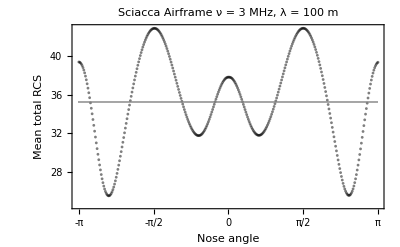

```mathematica
Do[
(* which measurement to grab *)
index=ν-2;
λ=Round[𝕔/(ν 1000000)];
rcs=meanRCS[[index]];
m=Length[rcs];
(* center nose angle *)
σ=RotateLeft[rcs,180];
μ=Mean[σ];
(* characterize data set *)
Print[lf,"frequency = ",ν," MHz (λ = ", λ, " m)"];
Print["mean rcs = ",μ];
(* plot mean value *)
gmean=Graphics[{Gray,Thin,Line[{{0,μ},{m,μ}}]}];
(* plot rcs *)
g000=ListPlot[σ,
Frame->True,
FrameTicks->fticks,
PlotStyle->{Black,Opacity[0.5],PointSize[0.005]},
FrameLabel->{sty["Nose angle"],sty["Mean total RCS"]},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},
PlotLabel->Style["Sciacca Airframe"<>lf<>"ν = "<>ToString[ν]<>" MHz, λ = "<>ToString[λ]<>" m",FontFamily->"TimesNewRoman"]];
gout=Show[{g000,gmean}];
,{ν,3,3}];
Show[{gout}]
```

## plot

## delete

#### maximum expansion order

```mathematica
ω=25;
```

```mathematica
avector=Table[Cos[j θ],{j,0,ω}];
bvector=Join[avector,Table[Sin[j θ],{j,ω}]];
```

```mathematica
masterA=Table[
Simplify[avector/.θ->Θ[[k]]]
,{k,m}];
```

### sweep

```mathematica
Do[
(* which measurement to grab *)
index=ν-2;
λ=Round[𝕔/(ν 1000000)];
rcs=meanRCS[[index]];
m=Length[rcs];
(* center nose angle *)
σ=RotateLeft[rcs,180];
(* characterize data set *)
μ=Mean[σ];
mx=Max[σ];
mn=Min[σ];
{top,bot}={1.1mx,0.9mn};Print[lf,"frequency = ",ν," MHz (λ = ", λ, " m)"];
Print["mean rcs = ",μ];
Print["variation bounded from ",mx," to ",mn];
(* scatter plot of data points *)
z={Θ,σ}ᵀ;
g000=ListPlot[z,PlotStyle->{Purple,Opacity[0.5],PointSize[0.005]}];
(* initializations *)
te={};
minTE=∞;
myAmplitudes={};
myErrors={};
G={};
(* sweep expansion orders *)
$tick;
Do[
(* define Hilbert space basis functions *)
vector=Take[avector,d+1];
(* grab slice of master matrix *)
A=Take[masterAᵀ,d+1]ᵀ;
(* compute Fourier-Bessel coefficients *)
c=LeastSquares[A,σ];
AppendTo[myAmplitudes,c];
(* approximation function *)
Clear[f];
f[θ_]=c.vector;
(* Print["f[θ] = ",f[θ]]; *)
(* approximation vector *)
F=f[θ]/.θ->Θ;
(* residual error *)
r=σ-F;
(* total error *)
r2=r.r;
If[r2<minTE,minTE=r2;where=d];
AppendTo[te,r2];
(* uncertainty propagation *)
ϵ=√(r2/(m-(d+1))Diagonal[Inverse[A†.A//N]]);
AppendTo[myErrors,ϵ];
(* signal to noise *)
γ=Last[c]/Last[ϵ];
AppendTo[G,{d,γ}];
(* function *)
g001=Plot[f[θ],{θ,-π,π},
Frame->True,
PlotRange->{bot,top},
FrameTicks->nticks,
PlotStyle->{Opacity[0.25],Blue}];
(* compare *)
ga=Show[{g001,g000},
PlotLabel->sty["MoM RCS vs Fourier Cosine Expansion"],
FrameLabel->{sty["Nose angle"],sty["Mean total RCS"]},
Epilog->{Text[sty["d = "<>ToString[d]],{0.95π,1.05mx},{1,0},Background->White],Text[sty["ν = "<>ToString[ν]<>" MHz λ = "<>ToString[λ]<>" m"],{-0.95π,1.05mx},{-1,0},Background->White]},
ImageSize->6 72];
(* residual error *)
gb=ListPlot[r,
Frame->True,
FrameTicks->fticks,
FrameLabel->{sty["Nose angle"],sty["Residual error"]},
PlotRange->Λ{-1,1},
PlotStyle->{Red,PointSize[0.005]},
PlotLabel->sty["Fourier Approximation Error"],
Epilog->{Text[sty["d = "<>ToString[d]],{350,0.80Λ},{1,0},Background->White],Text[sty["ν = "<>ToString[ν]<>" MHz, λ = "<>ToString[λ]<>" m"],{10,0.80Λ},{-1,0},Background->White]},
ImageSize->6 72];
(* spectrum *)
gc=ListPlot[r,
Frame->True,
FrameLabel->{sty["Term"],sty["Amplitude"]},
PlotStyle->{Blue,PointSize[0.005]},
PlotLabel->sty["Fourier Spectrum"],
ImageSize->6 72];
(* group plots *)
gout=GraphicsRow[{ga,gb},
ImageSize->14 72];
(* output *)
tresExport["spectrum-rcs-cos-"<>pad[ν]<>"-"<>pad[d],gc];
tresExport["fit-rcs-cos-"<>pad[ν]<>"-"<>pad[d],ga];
tresExport["rcs-cos-"<>pad[ν]<>"-"<>pad[d],gout];
,{d,0,ω}];
Print["minimum total error of ",minTE," at expansion order ",where];
(* aggregate paths *)
pTotalError=ListLogPlot[te,
Frame->True,
PlotStyle->Black,
ImageSize->6 72,
PlotLabel->Style["Mean Total RCS Approximation Error"<>lf<>"ν = "<>ToString[ν]<>" MHz, λ = "<>ToString[λ]<>" m",FontFamily->"TimesNewRoman"],
FrameLabel->{sty["Expansion order, d"],sty["Total Squared Error"]}
];
pSignalNoise=ListLogPlot[Abs[G],
Frame->True,
PlotStyle->Black,
ImageSize->6 72,
PlotLabel->Style["Mean Total RCS Highest Order Term"<>lf<>"ν = "<>ToString[ν]<>" MHz, λ = "<>ToString[λ]<>" m",FontFamily->"TimesNewRoman"],
FrameLabel->{sty["Expansion order, d"],sty["Signal to Noise"]}
];
(* output plots *)
tresExport["rcs-cos-total-error-"<>pad[ν]<>"-"<>pad[ω],pTotalError];
tresExport["rcs-cos-signal-to-noise-"<>pad[ν]<>"-"<>pad[ω],pSignalNoise];
tiempo["frequency = "<>ToString[ν]]
,{ν,3,30}];
```

minimum total error of 9.80907 at expansion order 25

frequency = 3
CPU time: 46.039 sec
elapsed time: 65.922163 sec

frequency = 4 MHz (λ = 75 m)

mean rcs = 19.9123

variation bounded from 38.1899 to 10.4888

minimum total error of 31.2546 at expansion order 25

frequency = 4
CPU time: 47.2065 sec
elapsed time: 70.799571 sec

frequency = 5 MHz (λ = 60 m)

mean rcs = 17.1993

variation bounded from 42.8299 to 1.98442

minimum total error of 39.8467 at expansion order 25

frequency = 5
CPU time: 47.2694 sec
elapsed time: 70.987247 sec

frequency = 6 MHz (λ = 50 m)

mean rcs = 16.853

variation bounded from 42.3212 to 3.0813

minimum total error of 41.5901 at expansion order 25

frequency = 6
CPU time: 47.2573 sec
elapsed time: 70.104723 sec

frequency = 7 MHz (λ = 43 m)

mean rcs = 17.0597

variation bounded from 32.6751 to 3.91808

minimum total error of 65.5368 at expansion order 25

frequency = 7
CPU time: 47.7689 sec
elapsed time: 74.907823 sec

frequency = 8 MHz (λ = 37 m)

mean rcs = 17.3469

variation bounded from 36.4519 to 3.70704

minimum total error of 87.8239 at expansion order 25

frequency = 8
CPU time: 47.767 sec
elapsed time: 69.477843 sec

frequency = 9 MHz (λ = 33 m)

mean rcs = 18.8395

variation bounded from 39.4069 to 3.35132

minimum total error of 153.165 at expansion order 25

frequency = 9
CPU time: 50.5388 sec
elapsed time: 79.551034 sec

frequency = 10 MHz (λ = 30 m)

mean rcs = 19.1984

variation bounded from 38.8539 to 3.72058

minimum total error of 174.402 at expansion order 25

frequency = 10
CPU time: 51.5409 sec
elapsed time: 86.058232 sec

frequency = 11 MHz (λ = 27 m)

mean rcs = 17.9797

variation bounded from 41.6111 to 2.48844

minimum total error of 200.554 at expansion order 25

frequency = 11
CPU time: 51.8404 sec
elapsed time: 84.338437 sec

frequency = 12 MHz (λ = 25 m)

mean rcs = 16.3034

variation bounded from 44.7781 to 0.798997

minimum total error of 343.652 at expansion order 25

frequency = 12
CPU time: 51.8398 sec
elapsed time: 84.090877 sec

frequency = 13 MHz (λ = 23 m)

mean rcs = 15.0111

variation bounded from 48.8126 to 1.9027

minimum total error of 584.69 at expansion order 25

frequency = 13
CPU time: 51.6016 sec
elapsed time: 83.962497 sec

frequency = 14 MHz (λ = 21 m)

mean rcs = 14.7227

variation bounded from 53.6002 to 3.69205

minimum total error of 733.084 at expansion order 25

frequency = 14
CPU time: 51.8795 sec
elapsed time: 83.025502 sec

frequency = 15 MHz (λ = 20 m)

mean rcs = 15.8665

variation bounded from 57.4762 to 3.21543

minimum total error of 800.364 at expansion order 25

frequency = 15
CPU time: 51.7374 sec
elapsed time: 83.325318 sec

frequency = 16 MHz (λ = 19 m)

mean rcs = 15.6994

variation bounded from 59.2522 to 3.38888

minimum total error of 859.255 at expansion order 25

frequency = 16
CPU time: 52.1204 sec
elapsed time: 83.202586 sec

frequency = 17 MHz (λ = 18 m)

mean rcs = 14.5658

variation bounded from 57.7514 to 1.64088

minimum total error of 1306.37 at expansion order 25

frequency = 17
CPU time: 51.6682 sec
elapsed time: 83.504097 sec

frequency = 18 MHz (λ = 17 m)

mean rcs = 14.7821

variation bounded from 54.0373 to 1.74348

minimum total error of 1616.32 at expansion order 25

frequency = 18
CPU time: 51.7283 sec
elapsed time: 83.198764 sec

frequency = 19 MHz (λ = 16 m)

mean rcs = 14.849

variation bounded from 50.3697 to 4.87629

minimum total error of 1476.6 at expansion order 25

frequency = 19
CPU time: 51.7993 sec
elapsed time: 80.376536 sec

frequency = 20 MHz (λ = 15 m)

mean rcs = 13.812

variation bounded from 48.4284 to 3.27238

minimum total error of 1219.72 at expansion order 25

frequency = 20
CPU time: 52.0968 sec
elapsed time: 84.600405 sec

frequency = 21 MHz (λ = 14 m)

mean rcs = 13.7212

variation bounded from 48.5161 to 1.61368

minimum total error of 1134.63 at expansion order 25

frequency = 21
CPU time: 52.2776 sec
elapsed time: 88.078185 sec

frequency = 22 MHz (λ = 14 m)

mean rcs = 13.6715

variation bounded from 49.6048 to 5.2553

minimum total error of 1287.13 at expansion order 25

frequency = 22
CPU time: 51.5141 sec
elapsed time: 76.760760 sec

frequency = 23 MHz (λ = 13 m)

mean rcs = 12.6693

variation bounded from 49.9665 to 4.30117

minimum total error of 1417.25 at expansion order 25

frequency = 23
CPU time: 51.8437 sec
elapsed time: 78.545477 sec

frequency = 24 MHz (λ = 12 m)

mean rcs = 12.5144

variation bounded from 49.9648 to 3.6458

minimum total error of 1575.24 at expansion order 25

frequency = 24
CPU time: 52.045 sec
elapsed time: 77.753931 sec

frequency = 25 MHz (λ = 12 m)

mean rcs = 13.1036

variation bounded from 50.8409 to 3.33106

minimum total error of 2255.03 at expansion order 25

frequency = 25
CPU time: 51.8128 sec
elapsed time: 77.646529 sec

frequency = 26 MHz (λ = 12 m)

mean rcs = 13.0431

variation bounded from 52.6271 to 3.2438

minimum total error of 2790.43 at expansion order 25

frequency = 26
CPU time: 52.4911 sec
elapsed time: 80.287011 sec

frequency = 27 MHz (λ = 11 m)

mean rcs = 12.7087

variation bounded from 53.3859 to 1.86151

minimum total error of 2727.41 at expansion order 25

frequency = 27
CPU time: 52.0826 sec
elapsed time: 81.048711 sec

frequency = 28 MHz (λ = 11 m)

mean rcs = 13.0194

variation bounded from 53.7889 to 2.46514

minimum total error of 3423.62 at expansion order 25

frequency = 28
CPU time: 52.1385 sec
elapsed time: 80.791508 sec

frequency = 29 MHz (λ = 10 m)

mean rcs = 12.7443

variation bounded from 54.1276 to 1.78411

minimum total error of 4599.82 at expansion order 25

frequency = 29
CPU time: 51.9315 sec
elapsed time: 80.819573 sec

frequency = 30 MHz (λ = 10 m)

mean rcs = 12.4426

variation bounded from 57.2657 to 2.69479

minimum total error of 5580.9 at expansion order 25

frequency = 30
CPU time: 52.2522 sec
elapsed time: 81.199955 sec

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```